```mathematica
ParametricPlot3D[{
{Sin[v],(1+Cos[v])Sin[u],(1+Cos[v])Cos[u]}
},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{Sin[v],(2+Cos[v])Sin[u],(2+Cos[v])Cos[u]}
},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
Integrate[x^2-y,x]
```

x^3/3-x y

```mathematica
Plot3D[x^3/3-x y,{x,-1.8047852466422523,1.8047852466422523},{y,-6.,6.}]
```

-Graphics3D-

```mathematica
Plot3D[x^3/3-x y,{x,y}∈Disk[{0,0},3],PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[x^3/3-x y,{x,y}∈Disk[{0,0},6],PlotRange->Full]
```

-Graphics3D-

```mathematica
Laplacian[x^3/3-x y,{x,y}]
```

2 x

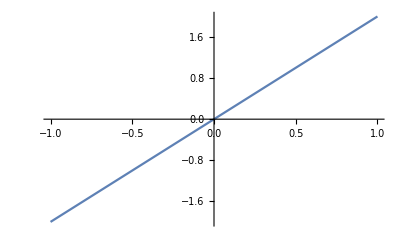

```mathematica
Plot[2 x,{x,-1,1}]
```

```mathematica
Show[{Plot3D[x^3/3-x y,{x,y}∈Disk[{0,0},6],PlotRange->Full],
Plot[2 x,{x,-1,1}]}]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics3D-,-Graphics-}]

```mathematica
Plot3D[
{x^3/3-x y,2x},
{x,y}∈Disk[{0,0},6],PlotRange->Full,ImageSize->Full,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
Div[x^3/3-x y,{x,y}]
```

Div::sclr: The scalar expression x^3/3-x y does not have a divergence.

(x^3/3-x y){x,y}

```mathematica
Grad[x^3/3-x y,{x,y}]
```

{x^2-y,-x}

```mathematica
Plot3D[
{x^3/3-x y,2x},
{x,y}∈Disk[{0,0},6],PlotRange->Full,PlotLegends->"Expressions"]
```

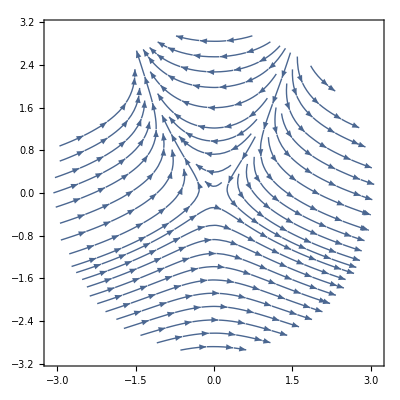

```mathematica
StreamPlot[{x^2-y,-x},{x,y}∈Disk[{0,0},3]]
```

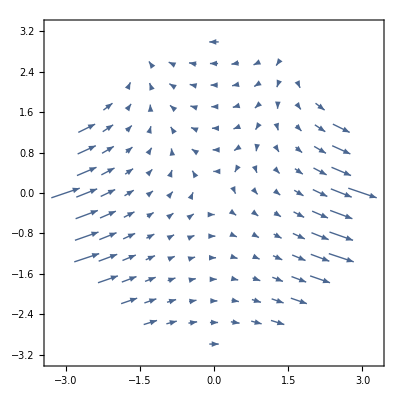

```mathematica
VectorPlot[{x^2-y,-x},{x,y}∈Disk[{0,0},3]]
```

```mathematica
VectorPlot3D[{x^2-y,-x,0},{x,y}∈Disk[{0,0},3]]
```

VectorPlot3D::idomdim: {x,y}∈Disk[{0,0},3] does not have a valid dimension as a plotting domain.

VectorPlot3D[{x^2-y,-x,0},{x,y}∈Disk[{0,0},3]]

```mathematica
DSolve[{x'[t]==x[t]^2-y[t],y'[t]==-x[t],x[0]==-1,y[0]==0},{x[t],y[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
DSolve[{x'[t]==1,y'[t]==-x[t],x[0]==-1,y[0]==0},{x[t],y[t]},{t}]
```

{{x[t]→-1+t,y[t]→1/2 (2 t-t^2)}}

```mathematica
DSolve[{x'[t]==x[t],y'[t]==-x[t],x[0]==-1,y[0]==0},{x[t],y[t]},{t}]
```

{{x[t]→-ⅇ^t,y[t]→-1+ⅇ^t}}

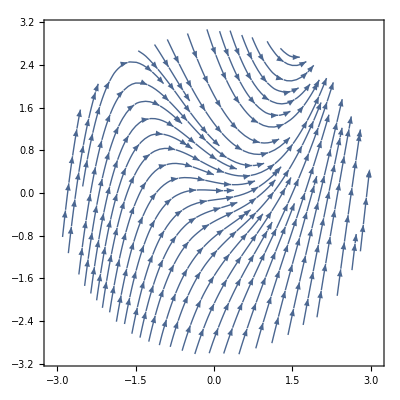

```mathematica
StreamPlot[{1,x^2-y},{x,y}∈Disk[{0,0},3]]
```

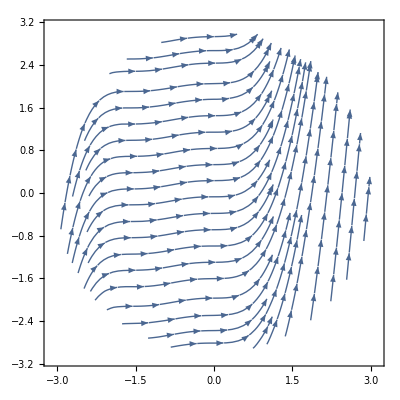

```mathematica
StreamPlot[{1,x^2 Sin[x]+x^2},{x,y}∈Disk[{0,0},3]]
```

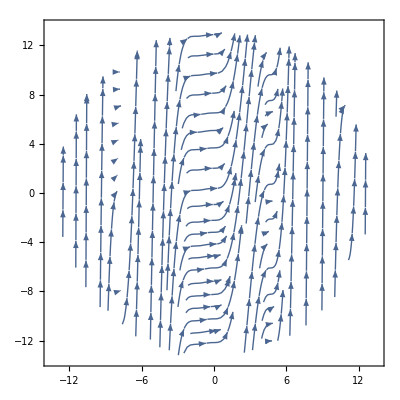

```mathematica
StreamPlot[{1,x^2 Sin[x]+x^2},{x,y}∈Disk[{0,0},13]]
```

```mathematica
DSolve[{x'[t]==1,y'[t]==x[t]^2 Sin[x[t]]+x[t]^2,x[0]==0,y[0]==0},{x[t],y[t]},{t}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -ArcCos[Cos[1]] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→t,y[t]→1/3 (-6+t^3+6 Cos[t]-3 t^2 Cos[t]+6 t Sin[t])}}

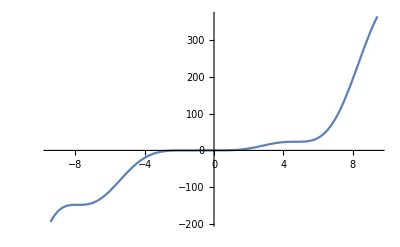

```mathematica
Plot[
1/3 (-6+t^3+6 Cos[t]-3 t^2 Cos[t]+6 t Sin[t]),
{t,-3π,3π}]
```

```mathematica
Manipulate[
Plot[
(1-a)t+a(1/3 (-6+t^3+6 Cos[t]-3 t^2 Cos[t]+6 t Sin[t])),
{t,-3π,3π}],
{a,0,1}]
```

```mathematica
Manipulate[
Plot[
(1-a)t+a(1/3 (-6+t^3+6 Cos[t]-3 t^2 Cos[t]+6 t Sin[t])),
{t,-3π,3π},PlotRange->{-400,400}],
{a,0,1}]
```

```mathematica
FullSimplify[Normalize@{t,1/3 (-6+t^3+6 Cos[t]-3 t^2 Cos[t]+6 t Sin[t])},t∈Reals]
```

{(3 t)/(√(9 t^2+(-6+t^3-3 (-2+t^2) Cos[t]+6 t Sin[t])^2)),(-6+t^3-3 (-2+t^2) Cos[t]+6 t Sin[t])/(√(9 t^2+(-6+t^3-3 (-2+t^2) Cos[t]+6 t Sin[t])^2))}

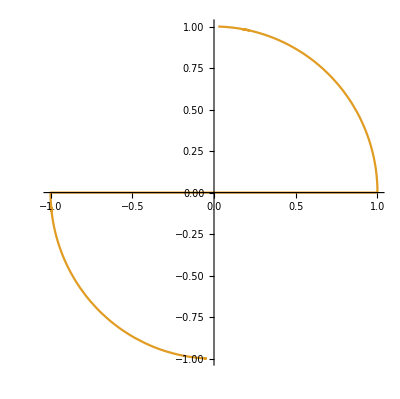

```mathematica
ParametricPlot[Out[29],{t,-3π,3π}]
```

```mathematica
D[x^2 Sin[x]+x^2,x]
```

2 x+x^2 Cos[x]+2 x Sin[x]

```mathematica
Simplify[2 x+x^2 Cos[x]+2 x Sin[x]]
```

x (2+x Cos[x]+2 Sin[x])

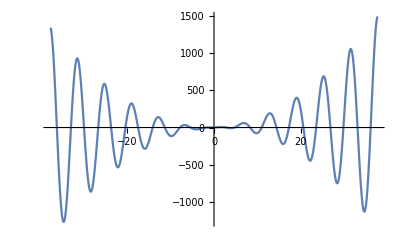

```mathematica
Plot[x (2+x Cos[x]+2 Sin[x]),{x,-37.69911184307752,37.69911184307752}]
```

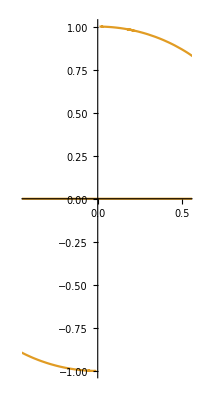

```mathematica
ParametricPlot[Out[29],{t,-5π,5π}]
```

```mathematica
D[x^2 Sin[x]+x^2,x]
```

2 x+x^2 Cos[x]+2 x Sin[x]

```mathematica
Exp[D[2^x,x]/2^x]
```

2

```mathematica
Exp[D[x^2 Sin[x]+x^2,x]/(x^2 Sin[x]+x^2)]
```

ⅇ^((2 x+x^2 Cos[x]+2 x Sin[x])/(x^2+x^2 Sin[x]))

```mathematica
FullSimplify[ⅇ^((2 x+x^2 Cos[x]+2 x Sin[x])/(x^2+x^2 Sin[x]))]
```

ⅇ^(2/x+1/(Sec[x]+Tan[x]))

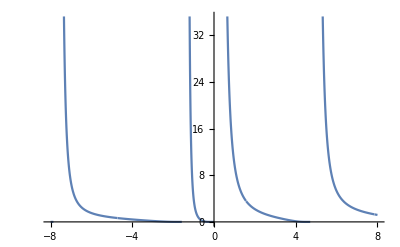

```mathematica
Plot[ⅇ^(2/x+1/(Sec[x]+Tan[x])),{x,-8,8}]
```

```mathematica
x (2+x Cos[x]+2 Sin[x])
```

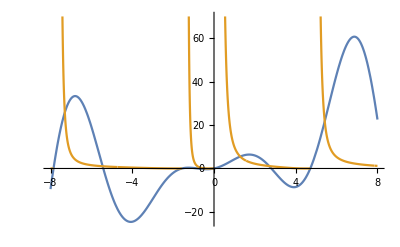

```mathematica
Plot[{x (2+x Cos[x]+2 Sin[x]),ⅇ^(2/x+1/(Sec[x]+Tan[x]))},{x,-8,8}]
```

```mathematica
x^2 Sin[x]+x^2
```

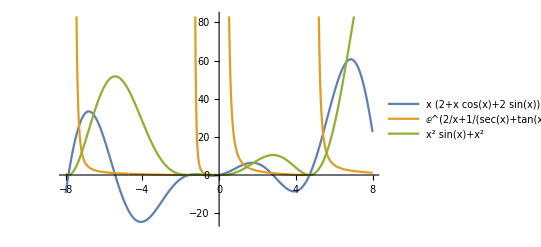

```mathematica
Plot[{x (2+x Cos[x]+2 Sin[x]),ⅇ^(2/x+1/(Sec[x]+Tan[x])),x^2 Sin[x]+x^2},{x,-8,8},PlotLegends->"Expressions"]
```

```mathematica
D[{x,x^2 Sin[x]+x^2,x},{x,2}].D[{x,x^2 Sin[x]+x^2,x},x]
```

(2 x+x^2 Cos[x]+2 x Sin[x]) (2+4 x Cos[x]+2 Sin[x]-x^2 Sin[x])

```mathematica
FullSimplify[(2 x+x^2 Cos[x]+2 x Sin[x]) (2+4 x Cos[x]+2 Sin[x]-x^2 Sin[x])]
```

x (2+x Cos[x]+2 Sin[x]) (2+4 x Cos[x]-(-2+x^2) Sin[x])

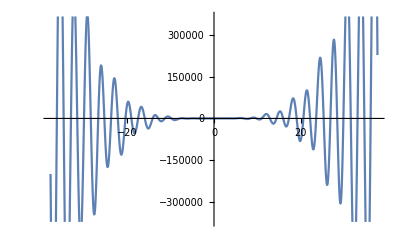

```mathematica
Plot[x (2+x Cos[x]+2 Sin[x]) (2+4 x Cos[x]-(-2+x^2) Sin[x]),{x,-37.69911184307752,37.69911184307752}]
```

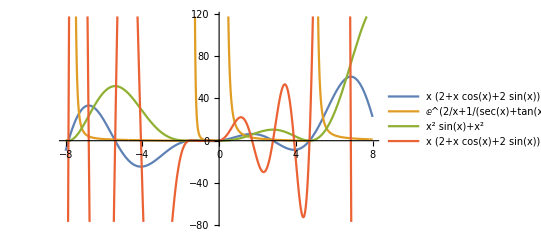

```mathematica
Plot[{
x (2+x Cos[x]+2 Sin[x]),
ⅇ^(2/x+1/(Sec[x]+Tan[x])),
x^2 Sin[x]+x^2,
x (2+x Cos[x]+2 Sin[x]) (2+4 x Cos[x]-(-2+x^2) Sin[x])
},{x,-8,8},
PlotLegends->"Expressions"]
```

```mathematica
circ={Cos[t],Sin[t]}
```

{Cos[t],Sin[t]}

```mathematica
D[circ,{t,2}].D[circ,t]
```

0

```mathematica
D[-f[x]Log[f[x]],f[x]]-D[D[-f[x]Log[f[x]],f'[x]],x]
```

-1-Log[f[x]]

```mathematica
D[-f[x]Log[f[x]],f[x]]-D[D[-f[x]Log[f[x]],f'[x]],x]==0
```

-1-Log[f[x]]==0

```mathematica
Reduce[-1-Log[f[x]]==0]
```

Log[f[x]]==-1

```mathematica
Solve[-1-Log[f[x]]==0,f[x]]
```

{{f[x]→1/ⅇ}}

```mathematica
With[{L=√(1+f'[x]^2)},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

(f'[x]^2 f''[x])/((1+f'[x]^2)^(3/2))-f''[x]/(√(1+f'[x]^2))==0

```mathematica
DSolve[(f'[x]^2 f''[x])/((1+f'[x]^2)^(3/2))-f''[x]/(√(1+f'[x]^2))==0,{f[x],f[x]},{x}]
```

{{f[x]→C[1]+x C[2]}}

```mathematica
With[{L=√(1+f'[x]^2)},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

```mathematica
With[{L=-f[x]Log[f[x]]},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

-1-Log[f[x]]==0

```mathematica
Entropy[f[x]]
```

Entropy::targ: Argument f[x] at position 1 should be a List, a SparseArray, or a String.

Entropy[f[x]]

```mathematica
Kurtosis[f[x]]
```

Kurtosis[f[x]]

```mathematica
With[{L=-f[x]Log[f[x]]-λ f[x]},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

-1-λ-Log[f[x]]==0

```mathematica
With[{L=f[x]^2},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

2 f[x]==0

```mathematica
With[{L=Integrate[f[x],x]},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

x==0

```mathematica
f''[x]f[x]
```

f[x] f''[x]

```mathematica
With[{f=Identity},
f''[x]f[x]]
```

0

```mathematica
With[{f=Sin},
f''[x]f[x]]
```

-Sin[x]^2

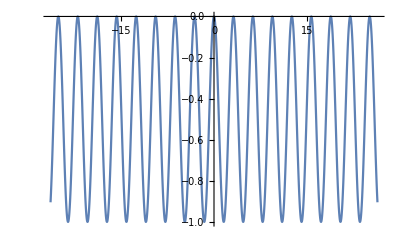

```mathematica
Plot[-Sin[x]^2,{x,-26.389378290154262,26.389378290154262}]
```

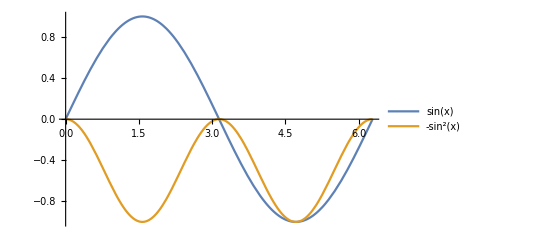

```mathematica
Plot[{Sin[x],-Sin[x]^2},{x,0,2 π},PlotLegends->"Expressions"]
```

```mathematica
-Sin[x]Log[Sin[x]]
```

-Log[Sin[x]] Sin[x]

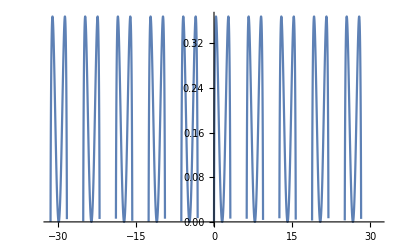

```mathematica
Plot[-Log[Sin[x]] Sin[x],{x,-10 π,10 π}]
```

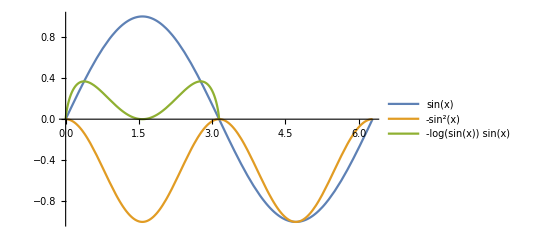

```mathematica
Plot[{Sin[x],-Sin[x]^2,-Log[Sin[x]] Sin[x]},{x,0,2 π},PlotLegends->"Expressions"]
```

```mathematica
-x Log[x]
```

-x Log[x]

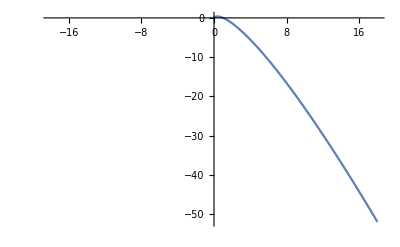

```mathematica
Plot[-x Log[x],{x,-18.,18.}]
```

```mathematica
Normalize@D[{t,Sin[t]},{t,2}].D[{t,Sin[t]},t]
```

-(Cos[t] Sin[t])/Abs[Sin[t]]

```mathematica
FullSimplify[
Normalize@D[{t,Sin[t]},{t,2}].D[{t,Sin[t]},t],t∈Reals]
```

-Cos[t] Sign[Sin[t]]

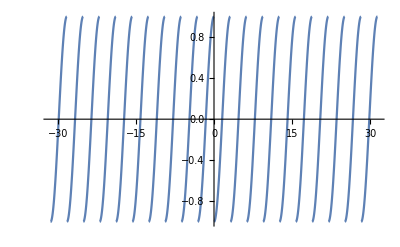

```mathematica
Plot[-Cos[t] Sign[Sin[t]],{t,-10 π,10 π}]
```

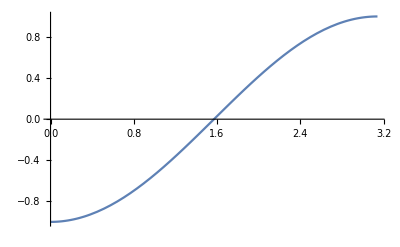

```mathematica
Plot[-Cos[t] Sign[Sin[t]],{t,0,1 π}]
```

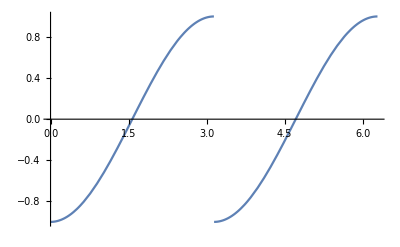

```mathematica
Plot[-Cos[t] Sign[Sin[t]],{t,0,2 π}]
```

```mathematica
Plot[-Cos[t] Sign[Sin[t]],{t,0,1 π}]
```

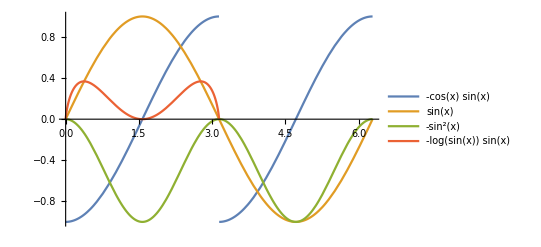

```mathematica
Plot[{-Cos[x] Sign[Sin[x]],Sin[x],-Sin[x]^2,-Log[Sin[x]] Sin[x]},{x,0,2π},PlotLegends->"Expressions"]
```

```mathematica
2 2x
```

4 x

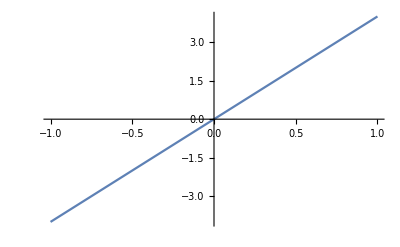

```mathematica
Plot[4 x,{x,-1,1}]
```

```mathematica
∫_0^∞ Exp[s t]f[t]ⅆt
```

∫_0^∞ ⅇ^(s t) f[t]ⅆt

```mathematica
Integrate[Exp[s t]f[t],t]
```

∫ⅇ^(s t) f[t]ⅆt

```mathematica
∫_0^∞ (Exp[-s t] t^a)ⅆt
```

ConditionalExpression[s^(-1-a) Gamma[1+a],Re[a]>-1&&Re[s]>0]

```mathematica
∫_0^∞ (Exp[-s t]Exp[t])ⅆt
```

ConditionalExpression[1/(-1+s),Re[s]>1]

```mathematica
LaplaceTransform[Exp[t],t,s]
```

1/(-1+s)

```mathematica
LaplaceTransform[Sin[t],t,s]
```

1/(1+s^2)

```mathematica
LaplaceTransform[t,t,s]
```

1/s^2

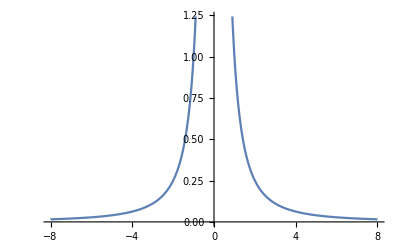

```mathematica
Plot[1/s^2,{s,-8,8}]
```

```mathematica
ComplexPlot[1/s^2,{x,-2ⅈ,2ⅈ}]
```

ComplexPlot::plld: Corners for x in {x,-2 ⅈ,2 ⅈ} must have distinct machine-precision real and imaginary parts.

ComplexPlot[1/s^2,{x,-2 ⅈ,2 ⅈ}]

```mathematica
ComplexPlot[1/s^2,{x,-2-2ⅈ,2+2ⅈ}]
```

-Graphics-

```mathematica
ReImPlot[1/s^2,{x,-2-2ⅈ,2+2ⅈ}]
```

ReImPlot::plln: Limiting value -2-2 ⅈ in {x,-2-2 ⅈ,2+2 ⅈ} is not a machine-sized real number.

ReImPlot[1/s^2,{x,-2-2 ⅈ,2+2 ⅈ}]

```mathematica
ComplexPlot[(z^2+1)/(z^2-1),{z,-2-2I,2+2I}]
```

-Graphics-

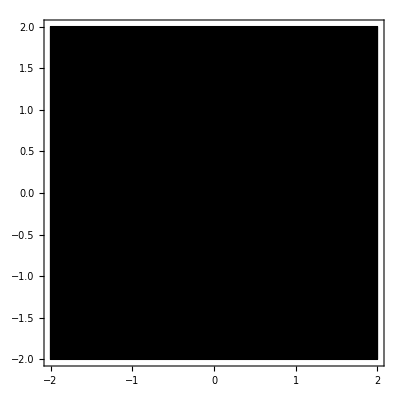

```mathematica
ComplexPlot[(z^2+1)/(z^2-1),{z,-2-2I,2+2I},PlotLegends->Automatic]
```

```mathematica
ComplexPlot[(z^2+1)/(z^2-1),{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ComplexPlot[1/(z^2-1),{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ComplexPlot[1/z^2,{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
Integrate[1/(√(1+x)),t]
```

t/(√(1+x))

```mathematica
Integrate[1/(√(1+x)),x]
```

2 √(1+x)

```mathematica
Integrate[1/(√(1+x^2)),x]
```

ArcSinh[x]

```mathematica
Integrate[1/(√(1+Sin[x])),x]
```

-((2+2 ⅈ) (-1)^(3/4) ArcTanh[(-1+Tan[x/4])/(√2)] (Cos[x/2]+Sin[x/2]))/(√(1+Sin[x]))

```mathematica
Integrate[x/(√(1+x)),x]
```

2/3 (-2+x) √(1+x)

```mathematica
Integrate[x/(√(1+x^2)),x]
```

√(1+x^2)

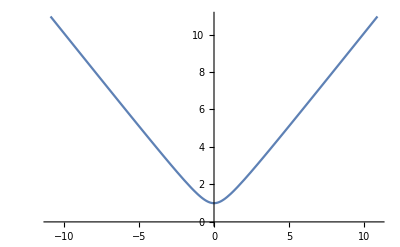

```mathematica
Plot[√(1+x^2),{x,-10.92,10.92}]
```

```mathematica
√(1+x^2)-x
```

-x+√(1+x^2)

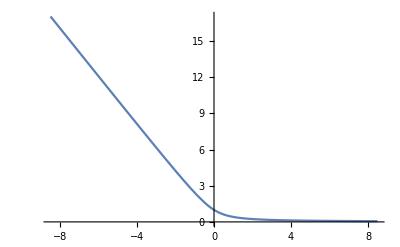

```mathematica
Plot[-x+√(1+x^2),{x,-8.493333333333334,8.493333333333334}]
```

```mathematica
√(1+x^2)
```

```mathematica
ComplexPlot[1/z^2,{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
LaplaceTransform[Sin[t],t,s]
```

-Graphics-

1/(1+s^2)

```mathematica
ComplexPlot[1/(1+s^2),{s,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ComplexPlot[1/(1+s^2),{s,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[Gamma[s],{s,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ComplexPlot[s,{s,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
LaplaceTransform[Exp[t],t,s]
```

1/(-1+s)

```mathematica
ComplexPlot[1/(-1+s),{s,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
LaplaceTransform[Sin[1/t],t,s]
```

MeijerG[{{},{}},{{1/2,1/2,1},{0}},s^2/16]/s

```mathematica
ComplexPlot[MeijerG[{{},{}},{{1/2,1/2,1},{0}},s^2/16]/s,{s,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

$Aborted

```mathematica
LaplaceTransform[Exp[t^2],t,s]
```

-1/2 ⅈ ⅇ^(-s^2/4) √π+DawsonF[s/2]

```mathematica
ComplexPlot[-1/2 ⅈ ⅇ^(-s^2/4) √π+DawsonF[s/2],{s,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
{Cos[t],Sin[t]}
```

{Cos[t],Sin[t]}

```mathematica
InverseFunction[Cos]
```

ArcCos

```mathematica
2Sin[ArcCos[t]]
```

2 √(1-t^2)

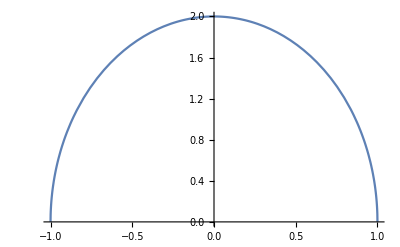

```mathematica
Plot[2 √(1-t^2),{t,-1,1}]
```

```mathematica
LaplaceTransform[1/(√t),t,s]
```

(√π)/(√s)

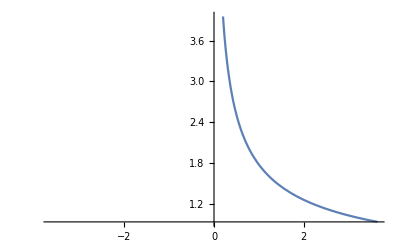

```mathematica
Plot[(√π)/(√s),{s,-3.64,3.64}]
```

```mathematica
ComplexPlot[(√π)/(√s),{s,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
LaplaceTransform[Gamma[t],t,s]
```

LaplaceTransform[Gamma[t],t,s]

```mathematica
LaplaceTransform[f[t],t,s]==λ f[t]
```

LaplaceTransform[f[t],t,s]==λ f[t]

```mathematica
Reduce[LaplaceTransform[f[t],t,s]==λ f[t]]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[LaplaceTransform[f[t],t,s]==λ f[t]]

```mathematica
LaplaceTransform[f[t],t,s]==λ f[t]
```

```mathematica
InverseLaplaceTransform[4/((s-1)^2(s^2+1)^2),s,t]
```

-2 ⅇ^t+ⅇ^t t+2 Cos[t]+Sin[t]+t Sin[t]

```mathematica
Simplify[-2 ⅇ^t+ⅇ^t t+2 Cos[t]+Sin[t]+t Sin[t]]
```

ⅇ^t (-2+t)+2 Cos[t]+(1+t) Sin[t]

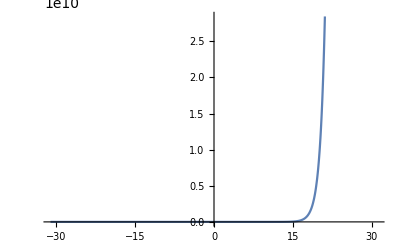

```mathematica
Plot[ⅇ^t (-2+t)+2 Cos[t]+(1+t) Sin[t],{t,-31.13274122871834,31.13274122871834}]
```

```mathematica
D[Exp[x],{x,2}]D[Exp[x],x]
```

ⅇ^(2 x)

```mathematica
Norm[Exp[2x]]
```

Norm[ⅇ^(2 x)]

```mathematica
Laplacian[Sin[α k],{α,k}]
```

-k^2 Sin[k α]-α^2 Sin[k α]

```mathematica
Simplify[-k^2 Sin[k α]-α^2 Sin[k α]]
```

-(k^2+α^2) Sin[k α]

```mathematica
TrigReduce[-(k^2+α^2) Sin[k α]]
```

-k^2 Sin[k α]-α^2 Sin[k α]

```mathematica
Simplify[-k^2 Sin[k α]-α^2 Sin[k α]]
```

-(k^2+α^2) Sin[k α]

```mathematica
ZTransform[-(k^2+α^2) Sin[k α],k,z]
```

-(z (1-6 z^2+z^4+α^2+4 z^2 α^2+z^4 α^2-2 z (1+z^2) (-1+2 α^2) Cos[α]+2 z^2 α^2 Cos[2 α]) Sin[α])/((1+z^2-2 z Cos[α])^3)

```mathematica
Manipulate[Plot[-(z (1-6 z^2+z^4+α^2+4 z^2 α^2+z^4 α^2-2 z (1+z^2) (-1+2 α^2) Cos[α]+2 z^2 α^2 Cos[2 α]) Sin[α])/((1+z^2-2 z Cos[α])^3),{z,-1.7531219802124722,1.8160229597893953}],{α,-3.02379941359882,1.1834823400891819}]
```

```mathematica
1/2∫_(-∞)^∞ (u[x,t]^2)ⅆx
```

1/2 ∫_(-∞)^∞ u[x,t]^2 ⅆx

```mathematica
1/2∫_(-∞)^∞ (u[x,t]^2)ⅆx
```

```mathematica
D[u[x,t],x]==D[u[x,t],{t,2}]
```

u^(1,0)[x,t]==u^(0,2)[x,t]

```mathematica
DSolve[{D[u[x,t],x]==D[u[x,t],{t,2}],u[x,0]==Sin[x]},{u[x,t]},{x,t}]
```

DSolve[{u^(1,0)[x,t]==u^(0,2)[x,t],u[x,0]==Sin[x]},{u[x,t]},{x,t}]

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Sin[x]},{u[x,t]},{x,t}]
```

{{u[x,t]→ⅇ^-t Sin[x]}}

```mathematica
Plot3D[ⅇ^-t Sin[x],{x,-2π,2π},{t,0,5}]
```

-Graphics3D-

```mathematica
Plot3D[ⅇ^-t Sin[x],{x,-2π,2π},{t,0,5},ColorFunction->"DarkRainbow",PlotRange->Full]
```

-Graphics3D-

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Sin[π x]},{u[x,t]},{x,t}]
```

{{u[x,t]→ⅇ^(-π^2 t) Sin[π x]}}

```mathematica
Plot3D[ⅇ^(-π^2 t) Sin[π x],{x,-2π,2π},{t,0,5},ColorFunction->"DarkRainbow",PlotRange->Full]
```

-Graphics3D-

```mathematica
1/2∫_(-∞)^∞ ((ⅇ^-t Sin[x])^2)ⅆx
```

1/2 ∫_(-∞)^∞ ⅇ^(-2 t) Sin[x]^2ⅆx

```mathematica
Integrate[(ⅇ^-t Sin[x])^2,x]
```

ⅇ^(-2 t) (x/2-1/4 Sin[2 x])

```mathematica
Plot3D[ⅇ^(-2 t) (x/2-1/4 Sin[2 x]),{t,-3.5986122886681096,3.5986122886681096},{x,-3.141592653589793,3.141592653589793},PlotRange->Full]
```

-Graphics3D-

```mathematica
Integrate[(ⅇ^-t Sin[x])^2,x]/2
```

1/2 ⅇ^(-2 t) (x/2-1/4 Sin[2 x])

```mathematica
Plot3D[1/2 ⅇ^(-2 t) (x/2-1/4 Sin[2 x]),{t,-10.549306144334055,10.549306144334055},{x,-3.141592653589793,3.141592653589793},PlotRange->Full]
```

-Graphics3D-

```mathematica
DSolve[{D[u[x,t],t]==1/16 D[u[x,t],{x,2}],u[x,0]==Exp[-x^2]},{u[x,t]},{x,t}]
```

{{u[x,t]→(2 ⅇ^(-(4 x^2)/(4+t)))/(√(4+t))}}

```mathematica
(2 ⅇ^(-(4 x^2)/(4+t)))/(√(4+t))
```

(2 ⅇ^(-(4 x^2)/(4+t)))/(√(4+t))

```mathematica
Plot3D[(2 ⅇ^(-(4 x^2)/(4+t)))/(√(4+t)),{t,-1.2107229567070348,1.2107229567070348},{x,-0.04621661640835095,0.04621661640835095}]
```

-Graphics3D-

```mathematica
Plot3D[(2 ⅇ^(-(4 x^2)/(4+t)))/(√(4+t)),{t,0,10},{x,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[(2 ⅇ^(-(4 x^2)/(4+t)))/(√(4+t)),{t,0,30},{x,-5,5},ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
DSolve[{D[u[x,t],t]==1/16 D[u[x,t],{x,2}],u[x,0]==Exp[-x^2],u[0,t]==0},{u[x,t]},{x,t}]
```

{{u[x,t]→Piecewise[{{(2 ⅇ^(-(4 x^2)/(4+t)) Erf[(4 x)/(√(t (4+t)))])/(√(4+t)), x>0}, {Indeterminate, True}}]}}

```mathematica
{{u[x,t]->Piecewise[{{(2 ⅇ^(-(4 x^2)/(4+t)) Erf[(4 x)/(√(t (4+t)))])/(√(4+t)),x>0}},Indeterminate]}}⟦1,1,2⟧
```

Piecewise[{{(2 ⅇ^(-(4 x^2)/(4+t)) Erf[(4 x)/(√(t (4+t)))])/(√(4+t)), x>0}, {Indeterminate, True}}]

```mathematica
Plot3D[Piecewise[{{(2 ⅇ^(-(4 x^2)/(4+t)) Erf[(4 x)/(√(t (4+t)))])/(√(4+t)),x>0}},Indeterminate],{t,-8,8},{x,-8,8}]
```

-Graphics3D-

```mathematica
Plot3D[Piecewise[{{(2 ⅇ^(-(4 x^2)/(4+t)) Erf[(4 x)/(√(t (4+t)))])/(√(4+t)),x>0}},Indeterminate],{t,-8,8},{x,-8,8},PlotRange->Full,ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}]+u[x,t]+f[x],u[0,t]==0,D[u[0,t],x]==0},{u[x,t]},{x,t}]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {u^(0,1)[x,t]==f[x]+u[x,t]+u^(2,0)[x,t],u[0,t]==0,True}.

DSolve[{u^(0,1)[x,t]==f[x]+u[x,t]+u^(2,0)[x,t],u[0,t]==0,True},{u[x,t]},{x,t}]

```mathematica
D[u[x,t],t]==D[u[x,t],{x,2}]+u[x,t]+f[x]
```

u^(0,1)[x,t]==f[x]+u[x,t]+u^(2,0)[x,t]

```mathematica
TreeForm@DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}]+u[x,t]+f[x],u[0,t]==0,D[u[0,t],x]==0},{u[x,t]},{x,t}]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {u^(0,1)[x,t]==f[x]+u[x,t]+u^(2,0)[x,t],u[0,t]==0,True}.

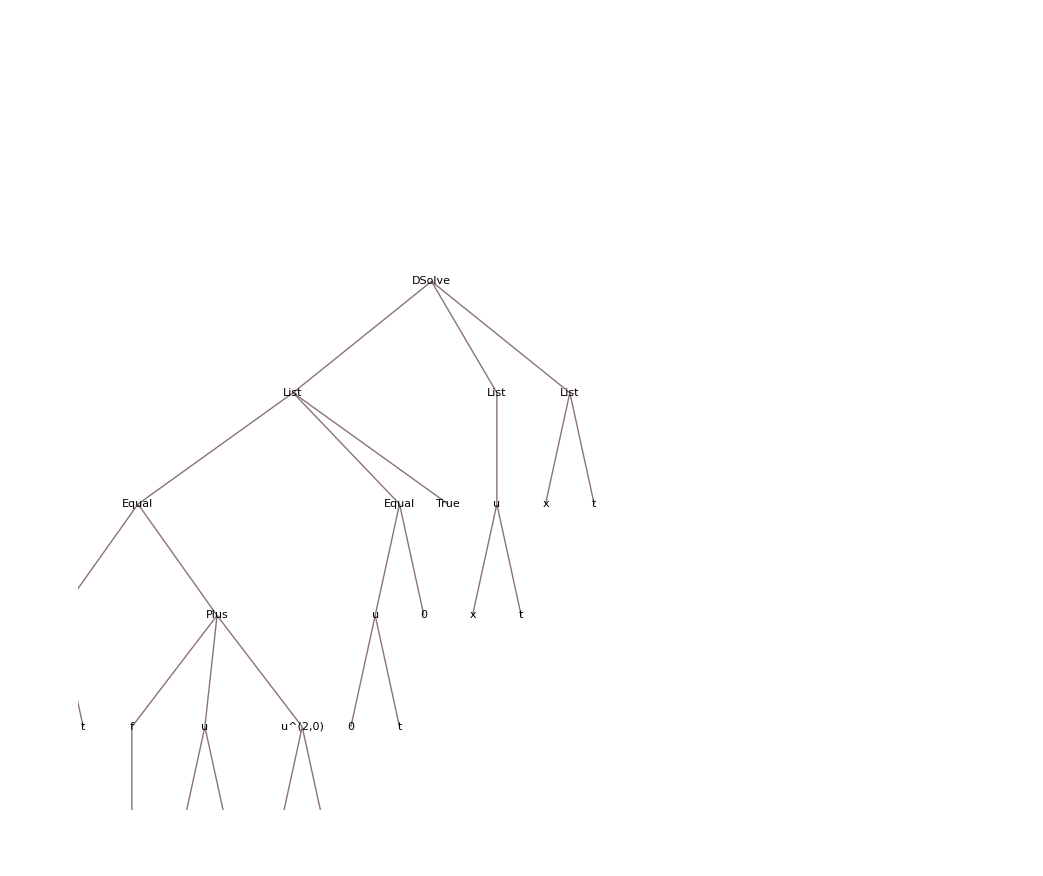

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}]+u[x,t]+f[x],u[0,t]==0,D[u[0,t],x]==0},{u[x,t]},{x,t}]
```

```mathematica
D[u[0,t],x]==0
```

True

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}]+u[x,t]+f[x],u[0,t]==0},{u[x,t]},{x,t}]
```

DSolve[{u^(0,1)[x,t]==f[x]+u[x,t]+u^(2,0)[x,t],u[0,t]==0},{u[x,t]},{x,t}]

```mathematica
x==0-1;x==√-1;x==Log[-1]
```

x==ⅈ π

```mathematica
x==Log[-1]
```

x==ⅈ π

```mathematica
Exp[x]==Exp[Log[-1]]
```

ⅇ^x==-1

```mathematica
ExampleData["Surface"]
```

ExampleData::notcoll: "Surface" is not a known collection for ExampleData. Use ExampleData[] for a list of collections.

ExampleData[Surface]

```mathematica
Entity["Surface","Sphere"]
```

sphere

```mathematica
SurfaceData[Entity["Surface","Sphere"],"RicciTensor"]
```

Function[a,Function[{u,v},{{a^2 Sin[v]^2,0},{0,a^2}}]]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"RiemannTensor"]
```

Function[a,Function[{u,v},{{{{0,0},{-0,0}},{{0,a^2},{-a^2,0}}},{{{0,-(a^2 Sin[v]^2)},{a^2 Sin[v]^2,0}},{{0,-0},{0,0}}}}]]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"SemialgebraicDescription"]
```

Missing[NotAvailable]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"SportObjects"]
```

{MLB baseball,FIBA men's basketball,FIBA women's basketball,NBA basketball,NCAA men's basketball,NCAA women's basketball,WNBA basketball,billiards ball,bludger,muggle bludger,bocce ball,bowling ball,candlepin bowling ball,Bruchenball,men's canoe polo ball,women's canoe polo ball,cricket ball,croquet ball,dodgeball,dodgeball blocker ball,dodgeball stinger ball,indoor field hockey ball,outdoor field hockey ball,futsal ball,Gaelic football,golf ball,rhythmic gymnastics ball,handball,size 3 korfball,size 4 korfball,size 5 korfball,NCAA men's lacrosse ball,NCAA women's lacrosse ball,men's netball,women's netball,pickleball ball,arena polo ball,outdoor polo ball,quaffle,muggle quaffle,racquetball,sliotar,11-inch slow pitch softball,12-inch slow pitch softball,snitch,muggle snitch,snooker ball,FIFA beach soccer ball,FIFA soccer ball,NCAA men's soccer ball,NCAA women's soccer ball,NCAA softball,squash ball,table tennis ball,tee ball,tennis ball type 1,tennis ball type 2,tennis ball type 3,tennis ball type high altitude,12-pound hammer,16-pound hammer,2-kilogram hammer,3-kilogram hammer,4-kilogram hammer,5-kilogram hammer,6-kilogram hammer,12-pound shot,16-pound shot,2-kilogram shot,3-kilogram shot,4-kilogram shot,5-kilogram shot,6-kilogram shot,6-pound shot,12-pound throwing weight,16-pound throwing weight,20-pound throwing weight,25-pound throwing weight,35-pound throwing weight,44-pound throwing weight,4-kilogram throwing weight,56-pound throwing weight,beach volleyball,indoor volleyball,FINA men's water polo ball,FINA women's water polo ball,wheelchair rugby ball}

```mathematica
SurfaceData[Entity["Surface","Sphere"],"Volume"]
```

Function[a,(4 π a^3)/3]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"NodeCount"]
```

0

```mathematica
SurfaceData[Entity["Surface","Sphere"],"NormalVector"]
```

Function[a,Function[{u,v},{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"MetricTensor"]
```

Function[a,Function[{u,v},{{a^2 Sin[v]^2,0},{0,a^2}}]]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"MeanCurvature"]
```

Function[a,Function[{u,v},1/a]]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"EulerCharacteristic"]
```

2

```mathematica
SurfaceData[Entity["Surface","Sphere"],"FirstFundamentalForm"]
```

Function[a,Function[{u,v},a^2 {Sin[v]^2,0,1}]]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"Centroid"]
```

Function[a,{0,0,0}]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"Genus"]
```

0

```mathematica
SurfaceData[Entity["Surface","Sphere"],"Image"]
```

-Graphics-

```mathematica
SurfaceData[Entity["Surface","Sphere"],"Image"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"GeneralizedDiameter"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"CartesianEquation"]
```

Function[a,Function[{x,y,z},x^2+y^2+z^2==a^2]]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"BoundingBox"]
```

Missing[UnknownProperty,{Surface,BoundingBox}]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"AssociatedPeople"]
```

{Euclid,Archimedes}

```mathematica
SurfaceData[Entity["Surface","Sphere"],"AlgebraicEquation"]
```

Function[a,Function[{x,y,z},x^2+y^2+z^2-a^2]]

```mathematica
SurfaceData[Entity["Surface","Sphere"],"GaussianCurvature"]
```

Function[a,Function[{u,v},1/a^2]]

```mathematica
Subsets@{a,b,c}
```

{{},{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
topology
]]
```

{{},{a,b,c}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},

]]
```

```mathematica
Through
```

```mathematica
FixedPoint[(#+2/#)/2&,1.]
```

1.41421

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Outer[f,topology,topology]
]]
```

{{},{{{},{f[a,a],f[a,b],f[a,c]}},{{},{f[b,a],f[b,b],f[b,c]}},{{},{f[c,a],f[c,b],f[c,c]}}}}

```mathematica
Outer
```

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Table[f[a,b],{a,topology},{b,topology}]
]]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {{},b,c}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {a,b,c}.

Table::iterb: Iterator {b,{{},{a,b,c}}} does not have appropriate bounds.

Table[f[a,b],{a,{{},{a,b,c}}},{b,{{},{a,b,c}}}]

```mathematica
Oute
```

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Table[f[a,b],{a,topology},{b,topology}]
]]
```

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Flatten[Outer[f,topology,topology],1]
]]
```

{{{},{f[a,a],f[a,b],f[a,c]}},{{},{f[b,a],f[b,b],f[b,c]}},{{},{f[c,a],f[c,b],f[c,c]}}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Table[
With[{a=topology[[i]],b=topology[[j]]},
1
],{a,1,Length@topology},{b,1,Length@topology}]
]]
```

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{{1,1},{1,1}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Table[
With[{a=topology[[i]],b=topology[[j]]},
f[a,b]
],{i,1,Length@topology},{j,1,Length@topology}]
]]
```

{{f[{},{}],f[{},{a,b,c}]},{f[{a,b,c},{}],f[{a,b,c},{a,b,c}]}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Table[
With[{a=topology[[i]],b=topology[[j]]},
{a,b}
],{i,1,Length@topology},{j,1,Length@topology}]
]]
```

{{{{},{}},{{},{a,b,c}}},{{{a,b,c},{}},{{a,b,c},{a,b,c}}}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Table[
With[{a=topology[[i]],b=topology[[j]]},
{a,b}->Intersection[a,b]
],{i,1,Length@topology},{j,1,Length@topology}]
]]
```

{{{{},{}}→{},{{},{a,b,c}}→{}},{{{a,b,c},{}}→{},{{a,b,c},{a,b,c}}→{a,b,c}}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Flatten[
Table[
With[{a=topology[[i]],b=topology[[j]]},
{a,b,Intersection[a,b]}
],{i,1,Length@topology},{j,1,Length@topology}],
1]
]]
```

{{{},{},{}},{{},{a,b,c},{}},{{a,b,c},{},{}},{{a,b,c},{a,b,c},{a,b,c}}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Flatten[
Table[
With[{a=topology[[i]],b=topology[[j]]},
{a,b,Intersection[a,b]}
],{i,1,Length@topology},{j,1,Length@topology}],
1]
]]
```

{} | {} | {}
{} | {a,b,c} | {}
{a,b,c} | {} | {}
{a,b,c} | {a,b,c} | {a,b,c}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Prepend[
Flatten[
Table[
With[{a=topology[[i]],b=topology[[j]]},
{a,b,Intersection[a,b]}
],{i,1,Length@topology},{j,1,Length@topology}],
1],
{Style["a",Bold],Style["b",Bold],Style["Intersection[a,b]",Bold]}]
]]
```

a | b | Intersection[a,b]
{} | {} | {}
{} | {a,b,c} | {}
{a,b,c} | {} | {}
{a,b,c} | {a,b,c} | {a,b,c}

```mathematica
Insert[Grid[{{Style["a",Bold],Style["b",Bold],Style["Intersection[a,b]",Bold]},{{},{},{}},{{},{a,b,c},{}},{{a,b,c},{},{}},{{a,b,c},{a,b,c},{a,b,c}}}],{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

a | b | Intersection[a,b]
{} | {} | {}
{} | {a,b,c} | {}
{a,b,c} | {} | {}
{a,b,c} | {a,b,c} | {a,b,c}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Prepend[
Flatten[
Table[
With[{a=topology[[i]],b=topology[[j]]},
{TraditionalForm@a,TraditionalForm@b,TraditionalForm@Intersection[a,b]}
],{i,1,Length@topology},{j,1,Length@topology}],
1],
{Style["a",Bold],Style["b",Bold],Style["Intersection[a,b]",Bold]}]
]]
```

a | b | Intersection[a,b]
{} | {} | {}
{} | {a,b,c} | {}
{a,b,c} | {} | {}
{a,b,c} | {a,b,c} | {a,b,c}

```mathematica
Subsets@{∅,U}
```

{{},{∅},{U},{∅,U}}

```mathematica
Union@Subsets@{∅,U}
```

{{},{U},{∅},{∅,U}}

```mathematica
Map[Union,Subsets@{∅,U}]
```

{{},{∅},{U},{U,∅}}

```mathematica
Range@10
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Subsets@Range@10
```

{{},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,2,9},{1,2,10},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,3,9},{1,3,10},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,4,9},{1,4,10},{1,5,6},{1,5,7},{1,5,8},{1,5,9},{1,5,10},{1,6,7},{1,6,8},{1,6,9},{1,6,10},{1,7,8},{1,7,9},{1,7,10},{1,8,9},{1,8,10},{1,9,10},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8},{2,3,9},{2,3,10},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,4,9},{2,4,10},{2,5,6},{2,5,7},{2,5,8},{2,5,9},{2,5,10},{2,6,7},{2,6,8},{2,6,9},{2,6,10},{2,7,8},{2,7,9},{2,7,10},{2,8,9},{2,8,10},{2,9,10},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,4,9},{3,4,10},{3,5,6},{3,5,7},{3,5,8},{3,5,9},{3,5,10},{3,6,7},{3,6,8},{3,6,9},{3,6,10},{3,7,8},{3,7,9},{3,7,10},{3,8,9},{3,8,10},{3,9,10},{4,5,6},{4,5,7},{4,5,8},{4,5,9},{4,5,10},{4,6,7},{4,6,8},{4,6,9},{4,6,10},{4,7,8},{4,7,9},{4,7,10},{4,8,9},{4,8,10},{4,9,10},{5,6,7},{5,6,8},{5,6,9},{5,6,10},{5,7,8},{5,7,9},{5,7,10},{5,8,9},{5,8,10},{5,9,10},{6,7,8},{6,7,9},{6,7,10},{6,8,9},{6,8,10},{6,9,10},{7,8,9},{7,8,10},{7,9,10},{8,9,10},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,3,7},{1,2,3,8},{1,2,3,9},{1,2,3,10},{1,2,4,5},{1,2,4,6},{1,2,4,7},{1,2,4,8},{1,2,4,9},{1,2,4,10},{1,2,5,6},{1,2,5,7},{1,2,5,8},{1,2,5,9},{1,2,5,10},{1,2,6,7},{1,2,6,8},{1,2,6,9},{1,2,6,10},{1,2,7,8},{1,2,7,9},{1,2,7,10},{1,2,8,9},{1,2,8,10},{1,2,9,10},{1,3,4,5},{1,3,4,6},{1,3,4,7},{1,3,4,8},{1,3,4,9},{1,3,4,10},{1,3,5,6},{1,3,5,7},{1,3,5,8},{1,3,5,9},{1,3,5,10},{1,3,6,7},{1,3,6,8},{1,3,6,9},{1,3,6,10},{1,3,7,8},{1,3,7,9},{1,3,7,10},{1,3,8,9},{1,3,8,10},{1,3,9,10},{1,4,5,6},{1,4,5,7},{1,4,5,8},{1,4,5,9},{1,4,5,10},{1,4,6,7},{1,4,6,8},{1,4,6,9},{1,4,6,10},{1,4,7,8},{1,4,7,9},{1,4,7,10},{1,4,8,9},{1,4,8,10},{1,4,9,10},{1,5,6,7},{1,5,6,8},{1,5,6,9},{1,5,6,10},{1,5,7,8},{1,5,7,9},{1,5,7,10},{1,5,8,9},{1,5,8,10},{1,5,9,10},{1,6,7,8},{1,6,7,9},{1,6,7,10},{1,6,8,9},{1,6,8,10},{1,6,9,10},{1,7,8,9},{1,7,8,10},{1,7,9,10},{1,8,9,10},{2,3,4,5},{2,3,4,6},{2,3,4,7},{2,3,4,8},{2,3,4,9},{2,3,4,10},{2,3,5,6},{2,3,5,7},{2,3,5,8},{2,3,5,9},{2,3,5,10},{2,3,6,7},{2,3,6,8},{2,3,6,9},{2,3,6,10},{2,3,7,8},{2,3,7,9},{2,3,7,10},{2,3,8,9},{2,3,8,10},{2,3,9,10},{2,4,5,6},{2,4,5,7},{2,4,5,8},{2,4,5,9},{2,4,5,10},{2,4,6,7},{2,4,6,8},{2,4,6,9},{2,4,6,10},{2,4,7,8},{2,4,7,9},{2,4,7,10},{2,4,8,9},{2,4,8,10},{2,4,9,10},{2,5,6,7},{2,5,6,8},{2,5,6,9},{2,5,6,10},{2,5,7,8},{2,5,7,9},{2,5,7,10},{2,5,8,9},{2,5,8,10},{2,5,9,10},{2,6,7,8},{2,6,7,9},{2,6,7,10},{2,6,8,9},{2,6,8,10},{2,6,9,10},{2,7,8,9},{2,7,8,10},{2,7,9,10},{2,8,9,10},{3,4,5,6},{3,4,5,7},{3,4,5,8},{3,4,5,9},{3,4,5,10},{3,4,6,7},{3,4,6,8},{3,4,6,9},{3,4,6,10},{3,4,7,8},{3,4,7,9},{3,4,7,10},{3,4,8,9},{3,4,8,10},{3,4,9,10},{3,5,6,7},{3,5,6,8},{3,5,6,9},{3,5,6,10},{3,5,7,8},{3,5,7,9},{3,5,7,10},{3,5,8,9},{3,5,8,10},{3,5,9,10},{3,6,7,8},{3,6,7,9},{3,6,7,10},{3,6,8,9},{3,6,8,10},{3,6,9,10},{3,7,8,9},{3,7,8,10},{3,7,9,10},{3,8,9,10},{4,5,6,7},{4,5,6,8},{4,5,6,9},{4,5,6,10},{4,5,7,8},{4,5,7,9},{4,5,7,10},{4,5,8,9},{4,5,8,10},{4,5,9,10},{4,6,7,8},{4,6,7,9},{4,6,7,10},{4,6,8,9},{4,6,8,10},{4,6,9,10},{4,7,8,9},{4,7,8,10},{4,7,9,10},{4,8,9,10},{5,6,7,8},{5,6,7,9},{5,6,7,10},{5,6,8,9},{5,6,8,10},{5,6,9,10},{5,7,8,9},{5,7,8,10},{5,7,9,10},{5,8,9,10},{6,7,8,9},{6,7,8,10},{6,7,9,10},{6,8,9,10},{7,8,9,10},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,7},{1,2,3,4,8},{1,2,3,4,9},{1,2,3,4,10},{1,2,3,5,6},{1,2,3,5,7},{1,2,3,5,8},{1,2,3,5,9},{1,2,3,5,10},{1,2,3,6,7},{1,2,3,6,8},{1,2,3,6,9},{1,2,3,6,10},{1,2,3,7,8},{1,2,3,7,9},{1,2,3,7,10},{1,2,3,8,9},{1,2,3,8,10},{1,2,3,9,10},{1,2,4,5,6},{1,2,4,5,7},{1,2,4,5,8},{1,2,4,5,9},{1,2,4,5,10},{1,2,4,6,7},{1,2,4,6,8},{1,2,4,6,9},{1,2,4,6,10},{1,2,4,7,8},{1,2,4,7,9},{1,2,4,7,10},{1,2,4,8,9},{1,2,4,8,10},{1,2,4,9,10},{1,2,5,6,7},{1,2,5,6,8},{1,2,5,6,9},{1,2,5,6,10},{1,2,5,7,8},{1,2,5,7,9},{1,2,5,7,10},{1,2,5,8,9},{1,2,5,8,10},{1,2,5,9,10},{1,2,6,7,8},{1,2,6,7,9},{1,2,6,7,10},{1,2,6,8,9},{1,2,6,8,10},{1,2,6,9,10},{1,2,7,8,9},{1,2,7,8,10},{1,2,7,9,10},{1,2,8,9,10},{1,3,4,5,6},{1,3,4,5,7},{1,3,4,5,8},{1,3,4,5,9},{1,3,4,5,10},{1,3,4,6,7},{1,3,4,6,8},{1,3,4,6,9},{1,3,4,6,10},{1,3,4,7,8},{1,3,4,7,9},{1,3,4,7,10},{1,3,4,8,9},{1,3,4,8,10},{1,3,4,9,10},{1,3,5,6,7},{1,3,5,6,8},{1,3,5,6,9},{1,3,5,6,10},{1,3,5,7,8},{1,3,5,7,9},{1,3,5,7,10},{1,3,5,8,9},{1,3,5,8,10},{1,3,5,9,10},{1,3,6,7,8},{1,3,6,7,9},{1,3,6,7,10},{1,3,6,8,9},{1,3,6,8,10},{1,3,6,9,10},{1,3,7,8,9},{1,3,7,8,10},{1,3,7,9,10},{1,3,8,9,10},{1,4,5,6,7},{1,4,5,6,8},{1,4,5,6,9},{1,4,5,6,10},{1,4,5,7,8},{1,4,5,7,9},{1,4,5,7,10},{1,4,5,8,9},{1,4,5,8,10},{1,4,5,9,10},{1,4,6,7,8},{1,4,6,7,9},{1,4,6,7,10},{1,4,6,8,9},{1,4,6,8,10},{1,4,6,9,10},{1,4,7,8,9},{1,4,7,8,10},{1,4,7,9,10},{1,4,8,9,10},{1,5,6,7,8},{1,5,6,7,9},{1,5,6,7,10},{1,5,6,8,9},{1,5,6,8,10},{1,5,6,9,10},{1,5,7,8,9},{1,5,7,8,10},{1,5,7,9,10},{1,5,8,9,10},{1,6,7,8,9},{1,6,7,8,10},{1,6,7,9,10},{1,6,8,9,10},{1,7,8,9,10},{2,3,4,5,6},{2,3,4,5,7},{2,3,4,5,8},{2,3,4,5,9},{2,3,4,5,10},{2,3,4,6,7},{2,3,4,6,8},{2,3,4,6,9},{2,3,4,6,10},{2,3,4,7,8},{2,3,4,7,9},{2,3,4,7,10},{2,3,4,8,9},{2,3,4,8,10},{2,3,4,9,10},{2,3,5,6,7},{2,3,5,6,8},{2,3,5,6,9},{2,3,5,6,10},{2,3,5,7,8},{2,3,5,7,9},{2,3,5,7,10},{2,3,5,8,9},{2,3,5,8,10},{2,3,5,9,10},{2,3,6,7,8},{2,3,6,7,9},{2,3,6,7,10},{2,3,6,8,9},{2,3,6,8,10},{2,3,6,9,10},{2,3,7,8,9},{2,3,7,8,10},{2,3,7,9,10},{2,3,8,9,10},{2,4,5,6,7},{2,4,5,6,8},{2,4,5,6,9},{2,4,5,6,10},{2,4,5,7,8},{2,4,5,7,9},{2,4,5,7,10},{2,4,5,8,9},{2,4,5,8,10},{2,4,5,9,10},{2,4,6,7,8},{2,4,6,7,9},{2,4,6,7,10},{2,4,6,8,9},{2,4,6,8,10},{2,4,6,9,10},{2,4,7,8,9},{2,4,7,8,10},{2,4,7,9,10},{2,4,8,9,10},{2,5,6,7,8},{2,5,6,7,9},{2,5,6,7,10},{2,5,6,8,9},{2,5,6,8,10},{2,5,6,9,10},{2,5,7,8,9},{2,5,7,8,10},{2,5,7,9,10},{2,5,8,9,10},{2,6,7,8,9},{2,6,7,8,10},{2,6,7,9,10},{2,6,8,9,10},{2,7,8,9,10},{3,4,5,6,7},{3,4,5,6,8},{3,4,5,6,9},{3,4,5,6,10},{3,4,5,7,8},{3,4,5,7,9},{3,4,5,7,10},{3,4,5,8,9},{3,4,5,8,10},{3,4,5,9,10},{3,4,6,7,8},{3,4,6,7,9},{3,4,6,7,10},{3,4,6,8,9},{3,4,6,8,10},{3,4,6,9,10},{3,4,7,8,9},{3,4,7,8,10},{3,4,7,9,10},{3,4,8,9,10},{3,5,6,7,8},{3,5,6,7,9},{3,5,6,7,10},{3,5,6,8,9},{3,5,6,8,10},{3,5,6,9,10},{3,5,7,8,9},{3,5,7,8,10},{3,5,7,9,10},{3,5,8,9,10},{3,6,7,8,9},{3,6,7,8,10},{3,6,7,9,10},{3,6,8,9,10},{3,7,8,9,10},{4,5,6,7,8},{4,5,6,7,9},{4,5,6,7,10},{4,5,6,8,9},{4,5,6,8,10},{4,5,6,9,10},{4,5,7,8,9},{4,5,7,8,10},{4,5,7,9,10},{4,5,8,9,10},{4,6,7,8,9},{4,6,7,8,10},{4,6,7,9,10},{4,6,8,9,10},{4,7,8,9,10},{5,6,7,8,9},{5,6,7,8,10},{5,6,7,9,10},{5,6,8,9,10},{5,7,8,9,10},{6,7,8,9,10},{1,2,3,4,5,6},{1,2,3,4,5,7},{1,2,3,4,5,8},{1,2,3,4,5,9},{1,2,3,4,5,10},{1,2,3,4,6,7},{1,2,3,4,6,8},{1,2,3,4,6,9},{1,2,3,4,6,10},{1,2,3,4,7,8},{1,2,3,4,7,9},{1,2,3,4,7,10},{1,2,3,4,8,9},{1,2,3,4,8,10},{1,2,3,4,9,10},{1,2,3,5,6,7},{1,2,3,5,6,8},{1,2,3,5,6,9},{1,2,3,5,6,10},{1,2,3,5,7,8},{1,2,3,5,7,9},{1,2,3,5,7,10},{1,2,3,5,8,9},{1,2,3,5,8,10},{1,2,3,5,9,10},{1,2,3,6,7,8},{1,2,3,6,7,9},{1,2,3,6,7,10},{1,2,3,6,8,9},{1,2,3,6,8,10},{1,2,3,6,9,10},{1,2,3,7,8,9},{1,2,3,7,8,10},{1,2,3,7,9,10},{1,2,3,8,9,10},{1,2,4,5,6,7},{1,2,4,5,6,8},{1,2,4,5,6,9},{1,2,4,5,6,10},{1,2,4,5,7,8},{1,2,4,5,7,9},{1,2,4,5,7,10},{1,2,4,5,8,9},{1,2,4,5,8,10},{1,2,4,5,9,10},{1,2,4,6,7,8},{1,2,4,6,7,9},{1,2,4,6,7,10},{1,2,4,6,8,9},{1,2,4,6,8,10},{1,2,4,6,9,10},{1,2,4,7,8,9},{1,2,4,7,8,10},{1,2,4,7,9,10},{1,2,4,8,9,10},{1,2,5,6,7,8},{1,2,5,6,7,9},{1,2,5,6,7,10},{1,2,5,6,8,9},{1,2,5,6,8,10},{1,2,5,6,9,10},{1,2,5,7,8,9},{1,2,5,7,8,10},{1,2,5,7,9,10},{1,2,5,8,9,10},{1,2,6,7,8,9},{1,2,6,7,8,10},{1,2,6,7,9,10},{1,2,6,8,9,10},{1,2,7,8,9,10},{1,3,4,5,6,7},{1,3,4,5,6,8},{1,3,4,5,6,9},{1,3,4,5,6,10},{1,3,4,5,7,8},{1,3,4,5,7,9},{1,3,4,5,7,10},{1,3,4,5,8,9},{1,3,4,5,8,10},{1,3,4,5,9,10},{1,3,4,6,7,8},{1,3,4,6,7,9},{1,3,4,6,7,10},{1,3,4,6,8,9},{1,3,4,6,8,10},{1,3,4,6,9,10},{1,3,4,7,8,9},{1,3,4,7,8,10},{1,3,4,7,9,10},{1,3,4,8,9,10},{1,3,5,6,7,8},{1,3,5,6,7,9},{1,3,5,6,7,10},{1,3,5,6,8,9},{1,3,5,6,8,10},{1,3,5,6,9,10},{1,3,5,7,8,9},{1,3,5,7,8,10},{1,3,5,7,9,10},{1,3,5,8,9,10},{1,3,6,7,8,9},{1,3,6,7,8,10},{1,3,6,7,9,10},{1,3,6,8,9,10},{1,3,7,8,9,10},{1,4,5,6,7,8},{1,4,5,6,7,9},{1,4,5,6,7,10},{1,4,5,6,8,9},{1,4,5,6,8,10},{1,4,5,6,9,10},{1,4,5,7,8,9},{1,4,5,7,8,10},{1,4,5,7,9,10},{1,4,5,8,9,10},{1,4,6,7,8,9},{1,4,6,7,8,10},{1,4,6,7,9,10},{1,4,6,8,9,10},{1,4,7,8,9,10},{1,5,6,7,8,9},{1,5,6,7,8,10},{1,5,6,7,9,10},{1,5,6,8,9,10},{1,5,7,8,9,10},{1,6,7,8,9,10},{2,3,4,5,6,7},{2,3,4,5,6,8},{2,3,4,5,6,9},{2,3,4,5,6,10},{2,3,4,5,7,8},{2,3,4,5,7,9},{2,3,4,5,7,10},{2,3,4,5,8,9},{2,3,4,5,8,10},{2,3,4,5,9,10},{2,3,4,6,7,8},{2,3,4,6,7,9},{2,3,4,6,7,10},{2,3,4,6,8,9},{2,3,4,6,8,10},{2,3,4,6,9,10},{2,3,4,7,8,9},{2,3,4,7,8,10},{2,3,4,7,9,10},{2,3,4,8,9,10},{2,3,5,6,7,8},{2,3,5,6,7,9},{2,3,5,6,7,10},{2,3,5,6,8,9},{2,3,5,6,8,10},{2,3,5,6,9,10},{2,3,5,7,8,9},{2,3,5,7,8,10},{2,3,5,7,9,10},{2,3,5,8,9,10},{2,3,6,7,8,9},{2,3,6,7,8,10},{2,3,6,7,9,10},{2,3,6,8,9,10},{2,3,7,8,9,10},{2,4,5,6,7,8},{2,4,5,6,7,9},{2,4,5,6,7,10},{2,4,5,6,8,9},{2,4,5,6,8,10},{2,4,5,6,9,10},{2,4,5,7,8,9},{2,4,5,7,8,10},{2,4,5,7,9,10},{2,4,5,8,9,10},{2,4,6,7,8,9},{2,4,6,7,8,10},{2,4,6,7,9,10},{2,4,6,8,9,10},{2,4,7,8,9,10},{2,5,6,7,8,9},{2,5,6,7,8,10},{2,5,6,7,9,10},{2,5,6,8,9,10},{2,5,7,8,9,10},{2,6,7,8,9,10},{3,4,5,6,7,8},{3,4,5,6,7,9},{3,4,5,6,7,10},{3,4,5,6,8,9},{3,4,5,6,8,10},{3,4,5,6,9,10},{3,4,5,7,8,9},{3,4,5,7,8,10},{3,4,5,7,9,10},{3,4,5,8,9,10},{3,4,6,7,8,9},{3,4,6,7,8,10},{3,4,6,7,9,10},{3,4,6,8,9,10},{3,4,7,8,9,10},{3,5,6,7,8,9},{3,5,6,7,8,10},{3,5,6,7,9,10},{3,5,6,8,9,10},{3,5,7,8,9,10},{3,6,7,8,9,10},{4,5,6,7,8,9},{4,5,6,7,8,10},{4,5,6,7,9,10},{4,5,6,8,9,10},{4,5,7,8,9,10},{4,6,7,8,9,10},{5,6,7,8,9,10},{1,2,3,4,5,6,7},{1,2,3,4,5,6,8},{1,2,3,4,5,6,9},{1,2,3,4,5,6,10},{1,2,3,4,5,7,8},{1,2,3,4,5,7,9},{1,2,3,4,5,7,10},{1,2,3,4,5,8,9},{1,2,3,4,5,8,10},{1,2,3,4,5,9,10},{1,2,3,4,6,7,8},{1,2,3,4,6,7,9},{1,2,3,4,6,7,10},{1,2,3,4,6,8,9},{1,2,3,4,6,8,10},{1,2,3,4,6,9,10},{1,2,3,4,7,8,9},{1,2,3,4,7,8,10},{1,2,3,4,7,9,10},{1,2,3,4,8,9,10},{1,2,3,5,6,7,8},{1,2,3,5,6,7,9},{1,2,3,5,6,7,10},{1,2,3,5,6,8,9},{1,2,3,5,6,8,10},{1,2,3,5,6,9,10},{1,2,3,5,7,8,9},{1,2,3,5,7,8,10},{1,2,3,5,7,9,10},{1,2,3,5,8,9,10},{1,2,3,6,7,8,9},{1,2,3,6,7,8,10},{1,2,3,6,7,9,10},{1,2,3,6,8,9,10},{1,2,3,7,8,9,10},{1,2,4,5,6,7,8},{1,2,4,5,6,7,9},{1,2,4,5,6,7,10},{1,2,4,5,6,8,9},{1,2,4,5,6,8,10},{1,2,4,5,6,9,10},{1,2,4,5,7,8,9},{1,2,4,5,7,8,10},{1,2,4,5,7,9,10},{1,2,4,5,8,9,10},{1,2,4,6,7,8,9},{1,2,4,6,7,8,10},{1,2,4,6,7,9,10},{1,2,4,6,8,9,10},{1,2,4,7,8,9,10},{1,2,5,6,7,8,9},{1,2,5,6,7,8,10},{1,2,5,6,7,9,10},{1,2,5,6,8,9,10},{1,2,5,7,8,9,10},{1,2,6,7,8,9,10},{1,3,4,5,6,7,8},{1,3,4,5,6,7,9},{1,3,4,5,6,7,10},{1,3,4,5,6,8,9},{1,3,4,5,6,8,10},{1,3,4,5,6,9,10},{1,3,4,5,7,8,9},{1,3,4,5,7,8,10},{1,3,4,5,7,9,10},{1,3,4,5,8,9,10},{1,3,4,6,7,8,9},{1,3,4,6,7,8,10},{1,3,4,6,7,9,10},{1,3,4,6,8,9,10},{1,3,4,7,8,9,10},{1,3,5,6,7,8,9},{1,3,5,6,7,8,10},{1,3,5,6,7,9,10},{1,3,5,6,8,9,10},{1,3,5,7,8,9,10},{1,3,6,7,8,9,10},{1,4,5,6,7,8,9},{1,4,5,6,7,8,10},{1,4,5,6,7,9,10},{1,4,5,6,8,9,10},{1,4,5,7,8,9,10},{1,4,6,7,8,9,10},{1,5,6,7,8,9,10},{2,3,4,5,6,7,8},{2,3,4,5,6,7,9},{2,3,4,5,6,7,10},{2,3,4,5,6,8,9},{2,3,4,5,6,8,10},{2,3,4,5,6,9,10},{2,3,4,5,7,8,9},{2,3,4,5,7,8,10},{2,3,4,5,7,9,10},{2,3,4,5,8,9,10},{2,3,4,6,7,8,9},{2,3,4,6,7,8,10},{2,3,4,6,7,9,10},{2,3,4,6,8,9,10},{2,3,4,7,8,9,10},{2,3,5,6,7,8,9},{2,3,5,6,7,8,10},{2,3,5,6,7,9,10},{2,3,5,6,8,9,10},{2,3,5,7,8,9,10},{2,3,6,7,8,9,10},{2,4,5,6,7,8,9},{2,4,5,6,7,8,10},{2,4,5,6,7,9,10},{2,4,5,6,8,9,10},{2,4,5,7,8,9,10},{2,4,6,7,8,9,10},{2,5,6,7,8,9,10},{3,4,5,6,7,8,9},{3,4,5,6,7,8,10},{3,4,5,6,7,9,10},{3,4,5,6,8,9,10},{3,4,5,7,8,9,10},{3,4,6,7,8,9,10},{3,5,6,7,8,9,10},{4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,8,9},{1,2,3,4,5,6,8,10},{1,2,3,4,5,6,9,10},{1,2,3,4,5,7,8,9},{1,2,3,4,5,7,8,10},{1,2,3,4,5,7,9,10},{1,2,3,4,5,8,9,10},{1,2,3,4,6,7,8,9},{1,2,3,4,6,7,8,10},{1,2,3,4,6,7,9,10},{1,2,3,4,6,8,9,10},{1,2,3,4,7,8,9,10},{1,2,3,5,6,7,8,9},{1,2,3,5,6,7,8,10},{1,2,3,5,6,7,9,10},{1,2,3,5,6,8,9,10},{1,2,3,5,7,8,9,10},{1,2,3,6,7,8,9,10},{1,2,4,5,6,7,8,9},{1,2,4,5,6,7,8,10},{1,2,4,5,6,7,9,10},{1,2,4,5,6,8,9,10},{1,2,4,5,7,8,9,10},{1,2,4,6,7,8,9,10},{1,2,5,6,7,8,9,10},{1,3,4,5,6,7,8,9},{1,3,4,5,6,7,8,10},{1,3,4,5,6,7,9,10},{1,3,4,5,6,8,9,10},{1,3,4,5,7,8,9,10},{1,3,4,6,7,8,9,10},{1,3,5,6,7,8,9,10},{1,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9},{2,3,4,5,6,7,8,10},{2,3,4,5,6,7,9,10},{2,3,4,5,6,8,9,10},{2,3,4,5,7,8,9,10},{2,3,4,6,7,8,9,10},{2,3,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,10},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,8,9,10},{1,2,3,4,5,7,8,9,10},{1,2,3,4,6,7,8,9,10},{1,2,3,5,6,7,8,9,10},{1,2,4,5,6,7,8,9,10},{1,3,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
Subsets@Range@3
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Map[Union,Subsets@Range@3]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Range@3
```

{1,2,3}

```mathematica
Norm@{1,2,3}
```

√14

```mathematica
2^(|{1,2,3}|)
```

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Prepend[
Flatten[
Table[
With[{a=topology[[i]],b=topology[[j]]},
{TraditionalForm@a,TraditionalForm@b,TraditionalForm@Intersection[a,b]}
],{i,1,Length@topology},{j,1,Length@topology}],
1],
{Style["a",Bold],Style["b",Bold],Style["Intersection[a,b]",Bold]}]
]]
```

a | b | Intersection[a,b]
{} | {} | {}
{} | {a,b,c} | {}
{a,b,c} | {} | {}
{a,b,c} | {a,b,c} | {a,b,c}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Prepend[
Flatten[
Table[
With[{a=topology[[i]],b=topology[[j]]},
{TraditionalForm@a,TraditionalForm@b,TraditionalForm@Intersection[a,b],Intersection[a,b]∈topology}
],{i,1,Length@topology},{j,1,Length@topology}],
1],
{Style["a",Bold],Style["b",Bold],Style["Intersection[a,b]",Bold],Style["∈ topology",Bold]}]
]]
```

a | b | Intersection[a,b] | ∈ topology
{} | {} | {} | True
{} | {a,b,c} | {} | True
{a,b,c} | {} | {} | True
{a,b,c} | {a,b,c} | {a,b,c} | {a,b,c}∈{{},{a,b,c}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Map[Apply[Union,#]&,Subsets@topology]
]]
```

{{},{},{a,b,c},{a,b,c}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Map[Apply[Union,#]&,Subsets@topology]
]]
```

```mathematica
All[True,True,False]
```

All[True,True,False]

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Map[{#,Apply[Union,#]}&,Subsets@topology]
]]
```

{{{},{}},{{{}},{}},{{{a,b,c}},{a,b,c}},{{{},{a,b,c}},{a,b,c}}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Map[{#,Apply[Union,#]}&,Subsets@topology]
]]
```

{} | {}
{{}} | {}
{{a,b,c}} | {a,b,c}
{{},{a,b,c}} | {a,b,c}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Prepend[
Map[{#,Apply[Union,#]}&,Subsets@topology],
{Style["Subset",Bold],Style["Intersection",Bold]}]
]]
```

Subset | Intersection
{} | {}
{{}} | {}
{{a,b,c}} | {a,b,c}
{{},{a,b,c}} | {a,b,c}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Prepend[
Map[{#,Apply[Union,#]}&,Subsets@topology],
{Style["Subset",Bold],Style["Intersection",Bold],Style["∈topology",Bold]}]
]]
```

Subset | Intersection | ∈topology
{} | {} | 
{{}} | {} | 
{{a,b,c}} | {a,b,c} | 
{{},{a,b,c}} | {a,b,c} |

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Prepend[
Map[{#,Apply[Union,#],Apply[Union,#]∈topology}&,Subsets@topology],
{Style["Subset",Bold],Style["Intersection",Bold],Style["∈topology",Bold]}]
]]
```

Subset | Intersection | ∈topology
{} | {} | True
{{}} | {} | True
{{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a,b,c}}
{{},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a,b,c}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
Grid@
Prepend[
Map[{#,Apply[Union,#],Element[Apply[Union,#],topology]}&,Subsets@topology],
{Style["Subset",Bold],Style["Intersection",Bold],Style["∈topology",Bold]}]
]]
```

Subset | Intersection | ∈topology
{} | {} | True
{{}} | {} | True
{{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a,b,c}}
{{},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a,b,c}}

```mathematica
a∈Rationals∧a∈Reals
```

a∈ℚ&&a∈ℝ

```mathematica
Reduce[a∈Rationals&&a∈Reals]
```

a∈ℚ

```mathematica
With[{set={a,b,c}},
With[{topology={{},set}},
{Grid@
Prepend[
Flatten[
Table[
With[{a=topology[[i]],b=topology[[j]]},
{TraditionalForm@a,TraditionalForm@b,TraditionalForm@Intersection[a,b],Intersection[a,b]∈topology}
],{i,1,Length@topology},{j,1,Length@topology}],
1],
{Style["a",Bold],Style["b",Bold],Style["Intersection[a,b]",Bold],Style["∈ topology",Bold]}],
Grid@
Prepend[
Map[{#,Apply[Union,#],Element[Apply[Union,#],topology]}&,Subsets@topology],
{Style["Subset",Bold],Style["Intersection",Bold],Style["∈topology",Bold]}]}
]]
```

{a | b | Intersection[a,b] | ∈ topology
{} | {} | {} | True
{} | {a,b,c} | {} | True
{a,b,c} | {} | {} | True
{a,b,c} | {a,b,c} | {a,b,c} | {a,b,c}∈{{},{a,b,c}},Subset | Intersection | ∈topology
{} | {} | True
{{}} | {} | True
{{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a,b,c}}
{{},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a,b,c}}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},{a},set}},
{Grid@
Prepend[
Flatten[
Table[
With[{a=topology[[i]],b=topology[[j]]},
{TraditionalForm@a,TraditionalForm@b,TraditionalForm@Intersection[a,b],Intersection[a,b]∈topology}
],{i,1,Length@topology},{j,1,Length@topology}],
1],
{Style["a",Bold],Style["b",Bold],Style["Intersection[a,b]",Bold],Style["∈ topology",Bold]}],
Grid@
Prepend[
Map[{#,Apply[Union,#],Element[Apply[Union,#],topology]}&,Subsets@topology],
{Style["Subset",Bold],Style["Intersection",Bold],Style["∈topology",Bold]}]}
]]
```

{a | b | Intersection[a,b] | ∈ topology
{} | {} | {} | True
{} | {a} | {} | True
{} | {a,b,c} | {} | True
{a} | {} | {} | True
{a} | {a} | {a} | {a}∈{{},{a},{a,b,c}}
{a} | {a,b,c} | {a} | {a}∈{{},{a},{a,b,c}}
{a,b,c} | {} | {} | True
{a,b,c} | {a} | {a} | {a}∈{{},{a},{a,b,c}}
{a,b,c} | {a,b,c} | {a,b,c} | {a,b,c}∈{{},{a},{a,b,c}},Subset | Intersection | ∈topology
{} | {} | True
{{}} | {} | True
{{a}} | {a} | {a}∈{{},{a},{a,b,c}}
{{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{a,b,c}}
{{},{a}} | {a} | {a}∈{{},{a},{a,b,c}}
{{},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{a,b,c}}
{{a},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{a,b,c}}
{{},{a},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{a,b,c}}}

```mathematica
With[{set={a,b,c}},
With[{topology={{},{a},{b},{c},set}},
{Grid@
Prepend[
Flatten[
Table[
With[{a=topology[[i]],b=topology[[j]]},
{TraditionalForm@a,TraditionalForm@b,TraditionalForm@Intersection[a,b],Intersection[a,b]∈topology}
],{i,1,Length@topology},{j,1,Length@topology}],
1],
{Style["a",Bold],Style["b",Bold],Style["Intersection[a,b]",Bold],Style["∈ topology",Bold]}],
Grid@
Prepend[
Map[{#,Apply[Union,#],Element[Apply[Union,#],topology]}&,Subsets@topology],
{Style["Subset",Bold],Style["Intersection",Bold],Style["∈topology",Bold]}]}
]]
```

{a | b | Intersection[a,b] | ∈ topology
{} | {} | {} | True
{} | {a} | {} | True
{} | {b} | {} | True
{} | {c} | {} | True
{} | {a,b,c} | {} | True
{a} | {} | {} | True
{a} | {a} | {a} | {a}∈{{},{a},{b},{c},{a,b,c}}
{a} | {b} | {} | True
{a} | {c} | {} | True
{a} | {a,b,c} | {a} | {a}∈{{},{a},{b},{c},{a,b,c}}
{b} | {} | {} | True
{b} | {a} | {} | True
{b} | {b} | {b} | {b}∈{{},{a},{b},{c},{a,b,c}}
{b} | {c} | {} | True
{b} | {a,b,c} | {b} | {b}∈{{},{a},{b},{c},{a,b,c}}
{c} | {} | {} | True
{c} | {a} | {} | True
{c} | {b} | {} | True
{c} | {c} | {c} | {c}∈{{},{a},{b},{c},{a,b,c}}
{c} | {a,b,c} | {c} | {c}∈{{},{a},{b},{c},{a,b,c}}
{a,b,c} | {} | {} | True
{a,b,c} | {a} | {a} | {a}∈{{},{a},{b},{c},{a,b,c}}
{a,b,c} | {b} | {b} | {b}∈{{},{a},{b},{c},{a,b,c}}
{a,b,c} | {c} | {c} | {c}∈{{},{a},{b},{c},{a,b,c}}
{a,b,c} | {a,b,c} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}},Subset | Intersection | ∈topology
{} | {} | True
{{}} | {} | True
{{a}} | {a} | {a}∈{{},{a},{b},{c},{a,b,c}}
{{b}} | {b} | {b}∈{{},{a},{b},{c},{a,b,c}}
{{c}} | {c} | {c}∈{{},{a},{b},{c},{a,b,c}}
{{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{a}} | {a} | {a}∈{{},{a},{b},{c},{a,b,c}}
{{},{b}} | {b} | {b}∈{{},{a},{b},{c},{a,b,c}}
{{},{c}} | {c} | {c}∈{{},{a},{b},{c},{a,b,c}}
{{},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{a},{b}} | {a,b} | {a,b}∈{{},{a},{b},{c},{a,b,c}}
{{a},{c}} | {a,c} | {a,c}∈{{},{a},{b},{c},{a,b,c}}
{{a},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{b},{c}} | {b,c} | {b,c}∈{{},{a},{b},{c},{a,b,c}}
{{b},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{c},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{a},{b}} | {a,b} | {a,b}∈{{},{a},{b},{c},{a,b,c}}
{{},{a},{c}} | {a,c} | {a,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{a},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{b},{c}} | {b,c} | {b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{b},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{c},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{a},{b},{c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{a},{b},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{a},{c},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{b},{c},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{a},{b},{c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{a},{b},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{a},{c},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{b},{c},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{a},{b},{c},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}
{{},{a},{b},{c},{a,b,c}} | {a,b,c} | {a,b,c}∈{{},{a},{b},{c},{a,b,c}}}